```mathematica
Get[NotebookDirectory[]<>#]&/@{
"23_10_04_parameters_1.m",
"23_10_04_simulation_1.m"
};
```

```mathematica
FvFmStyle={AxesOrigin->{18,0},AxesLabel->{"°C"},ImageSize->Medium,Ticks->Automatic,PlotRange->Full,LabelStyle->16,PlotRange->{{18,40},Automatic},ImagePadding->{{30,30},{25,20}}};
```

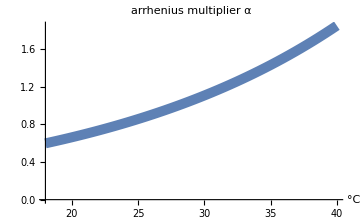

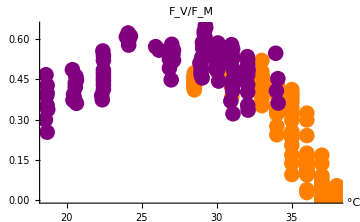
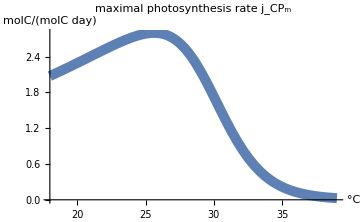

```mathematica
(Export[NotebookDirectory[]<>"export/Arrhenius.pdf",#];#)&@Plot[arr/.Q10Dino,{w,18,40},AxesLabel->{"°C",None},Evaluate@FvFmStyle,PlotStyle->Thickness[.02],PlotLabel->"arrhenius multiplier α"] 
(Export[NotebookDirectory[]<>"export/FvFmjCPm.pdf",#];#)&@Style[Row[{

Show[{
ListPlot[{FvFmpointsCunning2023,FvFmpointsBellworthy},PlotMarkers->({Graphics`PlotMarkers[][[1,1]],16}),PlotStyle->{Orange,Purple,Black},Evaluate@FvFmStyle,PlotLabel->Column[{"",Style["F_V/F_M",Italic]},Alignment->Center]](*,

Plot[FvFmFunc/.FvFmFIT["BestFitParameters"]/.Q10Dino,{w,18,39},PlotStyle->Thickness[.02],PlotRange->Full]*)},PlotRange->All],

Plot[jCPfuncArr/.toleranceFIT/.Q10Dino,{w,18,39},AxesLabel->{"°C",Style["molC/(molC day)",12]},Evaluate@FvFmStyle,PlotStyle->Thickness[.02],PlotLabel->Column[{"maximal photosynthesis rate","j_CP_m"},Alignment->Center]]},Spacer[15]],LineBreakWithin->False]
```